```mathematica
cellularFabrixDataset=Dataset[{Association["Cells"->8,"Racks"->0.5,"Bandwidth"->1600,"Latency"->2],Association["Cells"->16,"Racks"->1,"Bandwidth"->4800,"Latency"->50],Association["Cells"->32,"Racks"->2,"Bandwidth"->6400,"Latency"->100],Association["Cells"->64,"Racks"->4,"Bandwidth"->12800,"Latency"->150]}]
closNetworkDataset=Dataset[{Association["Bandwidth"->400,"Latency"->400],Association["Bandwidth"->1200,"Latency"->600],Association["Bandwidth"->1600,"Latency"->800],Association["Bandwidth"->3200,"Latency"->1200]}]
cellularBandwidth=cellularFabrixDataset[All,"Bandwidth"]
```

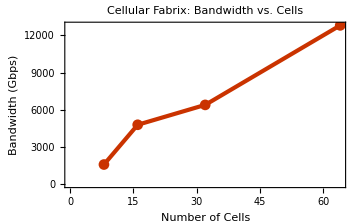

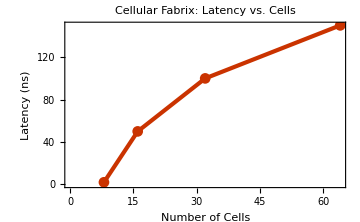

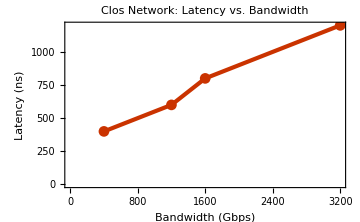

```mathematica
cellularFabrixDataset=Dataset[{Association["Cells"->8,"Racks"->0.5,"Bandwidth"->1600,"Latency"->2],Association["Cells"->16,"Racks"->1,"Bandwidth"->4800,"Latency"->50],Association["Cells"->32,"Racks"->2,"Bandwidth"->6400,"Latency"->100],Association["Cells"->64,"Racks"->4,"Bandwidth"->12800,"Latency"->150]}];
closNetworkDataset=Dataset[{Association["Bandwidth"->400,"Latency"->400],Association["Bandwidth"->1200,"Latency"->600],Association["Bandwidth"->1600,"Latency"->800],Association["Bandwidth"->3200,"Latency"->1200]}];
cellularBandwidthPlot=ListLinePlot[cellularFabrixDataset[All,{"Cells","Bandwidth"}],PlotLabel->"Cellular Fabrix: Bandwidth vs. Cells",AxesLabel->{"Number of Cells","Bandwidth (Gbps)"},PlotTheme->"Web",ImageSize->Medium,PlotMarkers->Automatic,LabelStyle->{Black,Bold}]
cellularLatencyPlot=ListLinePlot[cellularFabrixDataset[All,{"Cells","Latency"}],PlotLabel->"Cellular Fabrix: Latency vs. Cells",AxesLabel->{"Number of Cells","Latency (ns)"},PlotTheme->"Web",ImageSize->Medium,PlotMarkers->Automatic,LabelStyle->{Black,Bold}]
closNetworkPlot=ListLinePlot[closNetworkDataset[All,{"Bandwidth","Latency"}],PlotLabel->"Clos Network: Latency vs. Bandwidth",AxesLabel->{"Bandwidth (Gbps)","Latency (ns)"},PlotTheme->"Web",ImageSize->Medium,PlotMarkers->Automatic,LabelStyle->{Black,Bold}]
```

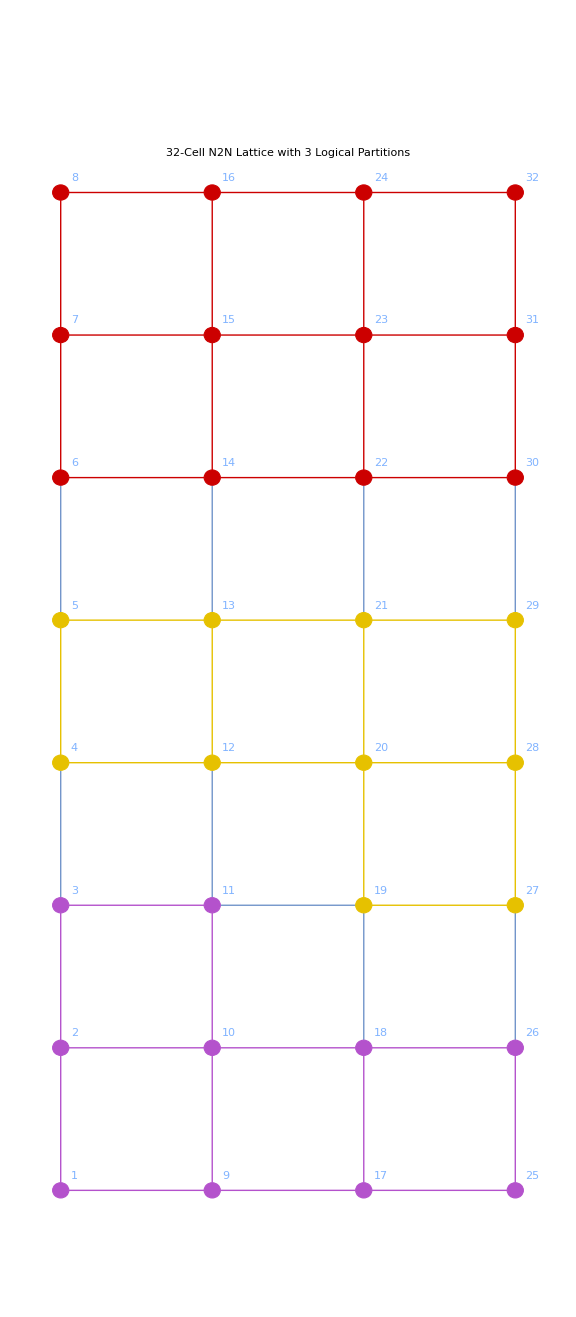

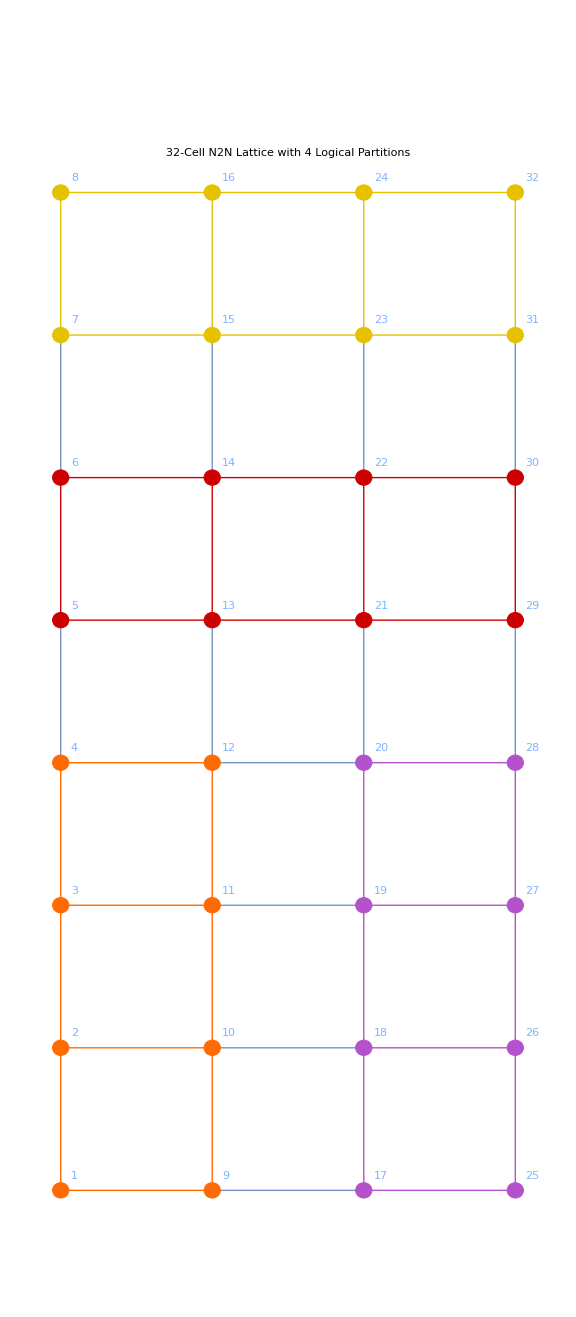

```mathematica
cellularFabrixGraph=GridGraph[{8,4},VertexLabels->"Name"];
threePartitions=FindGraphPartition[cellularFabrixGraph,3];
HighlightGraph[cellularFabrixGraph,(Subgraph[cellularFabrixGraph,#1]&)/@threePartitions,PlotLabel->"32-Cell N2N Lattice with 3 Logical Partitions",ImageSize->Large]
fourPartitions=FindGraphPartition[cellularFabrixGraph,4];
HighlightGraph[cellularFabrixGraph,(Subgraph[cellularFabrixGraph,#1]&)/@fourPartitions,PlotLabel->"32-Cell N2N Lattice with 4 Logical Partitions",ImageSize->Large]
```

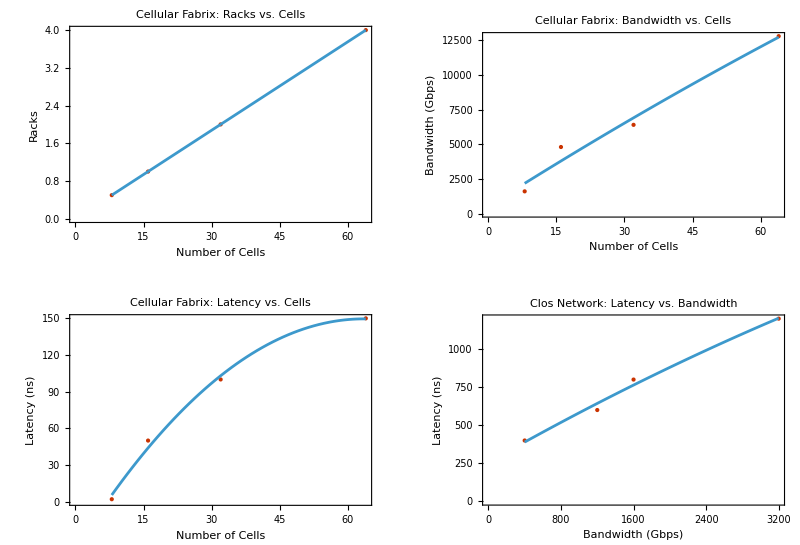

```mathematica
ClearAll["Global`*"];
cellularFabrixDataset=Dataset[{Association["Cells"->8,"Racks"->0.5,"Bandwidth"->1600,"Latency"->2],Association["Cells"->16,"Racks"->1,"Bandwidth"->4800,"Latency"->50],Association["Cells"->32,"Racks"->2,"Bandwidth"->6400,"Latency"->100],Association["Cells"->64,"Racks"->4,"Bandwidth"->12800,"Latency"->150]}];
closNetworkDataset=Dataset[{Association["Bandwidth"->400,"Latency"->400],Association["Bandwidth"->1200,"Latency"->600],Association["Bandwidth"->1600,"Latency"->800],Association["Bandwidth"->3200,"Latency"->1200]}];
toPairs[ds_,xKey_,yKey_]:=Normal[ds[All,{#1[xKey],#1[yKey]}&]];
racksData=toPairs[cellularFabrixDataset,"Cells","Racks"];
bandwidthData=toPairs[cellularFabrixDataset,"Cells","Bandwidth"];
latencyData=toPairs[cellularFabrixDataset,"Cells","Latency"];
closLatencyData=toPairs[closNetworkDataset,"Bandwidth","Latency"];
Clear[c,b];
racksFitExpr=Fit[racksData,{1,c},c];
bandwidthFitExpr=Fit[bandwidthData,{1,c,c^2},c];
latencyFitExpr=Fit[latencyData,{1,c,c^2},c];
closLatencyFitExpr=Fit[closLatencyData,{1,b,b^2},b];
xRange[data_]:={Min[First/@data],Max[First/@data]};
plotRacks=Show[ListPlot[racksData,PlotStyle->PointSize[Medium],AxesLabel->{"Number of Cells","Racks"},PlotLabel->"Cellular Fabrix: Racks vs. Cells",PlotTheme->"Web",LabelStyle->{Black,Bold}],Plot[racksFitExpr,{c,Sequence@@xRange[racksData]}]];
plotBandwidth=Show[ListPlot[bandwidthData,PlotStyle->PointSize[Medium],AxesLabel->{"Number of Cells","Bandwidth (Gbps)"},PlotLabel->"Cellular Fabrix: Bandwidth vs. Cells",PlotTheme->"Web",LabelStyle->{Black,Bold}],Plot[bandwidthFitExpr,{c,Sequence@@xRange[bandwidthData]}]];
plotLatency=Show[ListPlot[latencyData,PlotStyle->PointSize[Medium],AxesLabel->{"Number of Cells","Latency (ns)"},PlotLabel->"Cellular Fabrix: Latency vs. Cells",PlotTheme->"Web",LabelStyle->{Black,Bold}],Plot[latencyFitExpr,{c,Sequence@@xRange[latencyData]}]];
plotClosLatency=Show[ListPlot[closLatencyData,PlotStyle->PointSize[Medium],AxesLabel->{"Bandwidth (Gbps)","Latency (ns)"},PlotLabel->"Clos Network: Latency vs. Bandwidth",PlotTheme->"Web",LabelStyle->{Black,Bold}],Plot[closLatencyFitExpr,{b,Sequence@@xRange[closLatencyData]}]];
GraphicsGrid[{{plotRacks,plotBandwidth},{plotLatency,plotClosLatency}},ImageSize->Full]
```

```mathematica
Manipulate[propagationSpeed=200000000;transmissionTime=(packetSize 8)/(linkSpeed 1000000000);packetLengthOnWire=transmissionTime propagationSpeed;propagationDelay=linkLength/propagationSpeed;roundTripTime=2 propagationDelay;isPipelined=transmissionTime>roundTripTime;Animate[Module[{dataHead,dataTail,ackHead,ackTail,statusText,statusColor},dataHead=Min[propagationSpeed t,linkLength];dataTail=Max[0,dataHead-packetLengthOnWire];ackHead=If[t>propagationDelay,Max[0,linkLength-propagationSpeed (t-propagationDelay)],linkLength];ackTail=Min[linkLength,ackHead+1];statusText=Which[t<propagationDelay,"Transmitting...",t<transmissionTime&&t>propagationDelay,"Data Arriving... Sending SACK",t>transmissionTime&&ackHead>0,"Receiving Pipelined ACK",True,"Interaction Complete"];statusColor=If[isPipelined,Darker[Green],Orange];Graphics[{Text[Style["Sender (Alice)",Bold,12],{-linkLength 0.1,0},{1,0}],FaceForm[GrayLevel[0.9]],EdgeForm[Black],Rectangle[{-linkLength 0.05,-0.1},{0,0.1}],Text[Style["Receiver (Bob)",Bold,12],{linkLength 1.1,0},{-1,0}],Rectangle[{linkLength,-0.1},{linkLength 1.05,0.1}],{Gray,Thickness[0.002],Line[{{0,0.05},{linkLength,0.05}}]},{Gray,Thickness[0.002],Line[{{0,-0.05},{linkLength,-0.05}}]},If[dataTail<linkLength,{Darker[Green],Rectangle[{dataTail,0.025},{dataHead,0.075}]}],If[t>propagationDelay&&ackHead>0,{Darker[Blue],Rectangle[{ackHead,-0.075},{ackTail,-0.025}]}],Text[Style["Transmission Time: "<>ToString[NumberForm[transmissionTime 1000000000,{3,2}]]<>" ns",12],{linkLength/2,0.4}],Text[Style["Round-Trip Time: "<>ToString[NumberForm[roundTripTime 1000000000,{3,2}]]<>" ns",12],{linkLength/2,0.3}],Text[Style["Packet Length on Wire: "<>ToString[NumberForm[packetLengthOnWire,{3,2}]]<>" m",12],{linkLength/2,0.2}],If[isPipelined&&t>roundTripTime,Text[Style["PIPELINED ACK ACHIEVED",Bold,16,Darker[Green]],{linkLength/2,-0.3}],Text[Style["Stop-and-Wait Behavior",Bold,16,Gray],{linkLength/2,-0.3}]]},PlotRange->{{-linkLength 0.2,linkLength 1.2},{-0.5,0.5}},ImageSize->Large,GridLines->{Range[0,linkLength,linkLength/10],None},AspectRatio->1/3,PlotLabel->Style["Æthernet Link: Pipelined vs. Stop-and-Wait",Bold,16]]],{t,0,2 (transmissionTime+propagationDelay)},AnimationRate->1,DisplayAllSteps->True],Grid[{{Style["Link Length (m)",Bold],Manipulator[Dynamic[linkLength],{1,200,1},ImageSize->Small],Dynamic[linkLength]},{Style["Packet Size (bytes)",Bold],Manipulator[Dynamic[packetSize],{64,4096,8},ImageSize->Small],Dynamic[packetSize]},{Style["Link Speed (Gbps)",Bold],Manipulator[Dynamic[linkSpeed],{10,400,10},ImageSize->Small],Dynamic[linkSpeed]}},Alignment->Left],ControlPlacement->Top,TrackedSymbols:>{linkLength,packetSize,linkSpeed}]
```

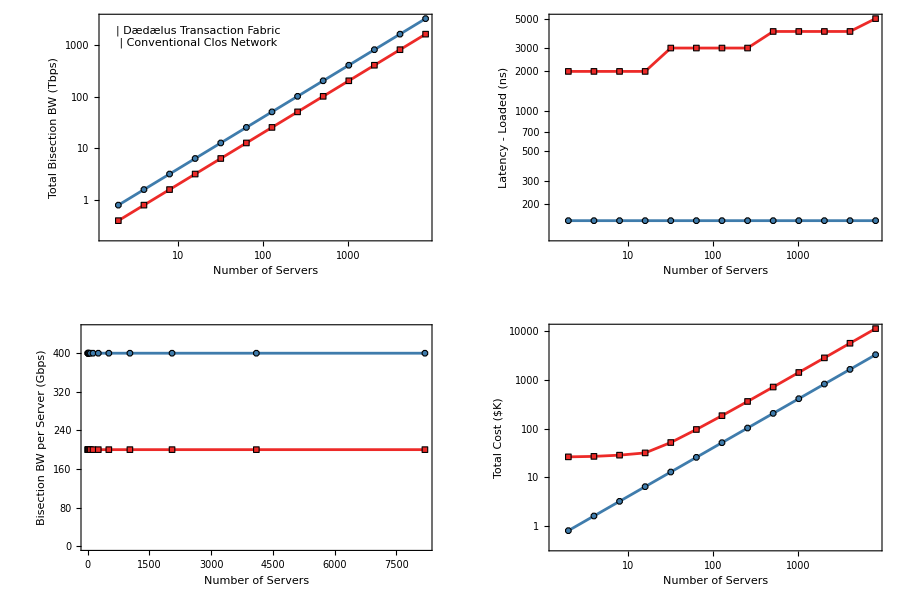

```mathematica
daeData=Association["# Servers"->{2,4,8,16,32,64,128,256,512,1024,2048,4096,8192},"Total Bisection BW (Tbps)"->{0.8,1.6,3.2,6.4,12.8,25.6,51.2,102.4,204.8,409.6,819.2,1638.4,3276.8},"Bisection BW per Server (Gbps)"->{400,400,400,400,400,400,400,400,400,400,400,400,400},"Latency - Unloaded (ns)"->{50,50,50,50,50,50,50,50,50,50,50,50,50},"Latency - Loaded (ns)"->{150,150,150,150,150,150,150,150,150,150,150,150,150},"Total Cost ($K)"->{0.8,1.6,3.2,6.4,12.8,25.6,51.2,102.4,204.8,409.6,819.2,1638.4,3276.8}];
closData=Association["# Servers"->{2,4,8,16,32,64,128,256,512,1024,2048,4096,8192},"Total Bisection BW (Tbps)"->{0.4,0.8,1.6,3.2,6.4,12.8,25.6,51.2,102.4,204.8,409.6,819.2,1638.4},"Bisection BW per Server (Gbps)"->{200,200,200,200,200,200,200,200,200,200,200,200,200},"Latency - Unloaded (ns)"->{500,500,500,500,900,900,900,900,1300,1300,1300,1300,1700},"Latency - Loaded (ns)"->{2000,2000,2000,2000,3000,3000,3000,3000,4000,4000,4000,4000,5000},"Total Cost ($K)"->{26.2,26.8,28.4,31.6,51.6,95.6,183.6,359.6,711.6,1415.6,2823.6,5639.6,11271.6}];
servers=daeData["# Servers"];
dataSeries=Association["DAE BW"->Transpose[{servers,daeData["Total Bisection BW (Tbps)"]}],"CLOS BW"->Transpose[{servers,closData["Total Bisection BW (Tbps)"]}],"DAE Latency"->Transpose[{servers,daeData["Latency - Loaded (ns)"]}],"CLOS Latency"->Transpose[{servers,closData["Latency - Loaded (ns)"]}],"DAE Cost"->Transpose[{servers,daeData["Total Cost ($K)"]}],"CLOS Cost"->Transpose[{servers,closData["Total Cost ($K)"]}],"DAE BW/Server"->Transpose[{servers,daeData["Bisection BW per Server (Gbps)"]}],"CLOS BW/Server"->Transpose[{servers,closData["Bisection BW per Server (Gbps)"]}]];
colorlist={RGBColor["#3F7CAC"],RGBColor["#ED2A28"],RGBColor["#F6A13A"],RGBColor["#9E9E49"]};
daeMarker={Graphics[{colorlist⟦1⟧,EdgeForm[Black],RegularPolygon[8]}],Scaled[0.03]};
closMarker={Graphics[{colorlist⟦2⟧,EdgeForm[Black],RegularPolygon[4]}],Scaled[0.025]};
legend=Grid[{{Graphics[{daeMarker⟦1,1⟧},ImageSize->20],Style["Dædælus Transaction Fabric",12]},{Graphics[{closMarker⟦1,1⟧},ImageSize->20],Style["Conventional Clos Network",12]}},Alignment->Left,Spacings->{1,0.5}];
bwPlot=ListLogLogPlot[{dataSeries["DAE BW"],dataSeries["CLOS BW"]},Joined->True,PlotStyle->{colorlist⟦1⟧,colorlist⟦2⟧},PlotMarkers->{daeMarker,closMarker},Frame->True,FrameLabel->{"Number of Servers","Total Bisection BW (Tbps)"},LabelStyle->Directive[Black,12,FontFamily->"Myriad Pro"],FrameStyle->Directive[Black,Thickness[.002]],Axes->False,Epilog->Inset[Framed[legend,RoundingRadius->5],Scaled[{0.05,0.95}],{Left,Top}]];
latencyPlot=ListLogLogPlot[{dataSeries["DAE Latency"],dataSeries["CLOS Latency"]},Joined->True,PlotStyle->{colorlist⟦1⟧,colorlist⟦2⟧},PlotMarkers->{daeMarker,closMarker},Frame->True,FrameLabel->{"Number of Servers","Latency - Loaded (ns)"},LabelStyle->Directive[Black,12,FontFamily->"Myriad Pro"],FrameStyle->Directive[Black,Thickness[.002]],Axes->False,PlotRange->All];
costPlot=ListLogLogPlot[{dataSeries["DAE Cost"],dataSeries["CLOS Cost"]},Joined->True,PlotStyle->{colorlist⟦1⟧,colorlist⟦2⟧},PlotMarkers->{daeMarker,closMarker},Frame->True,FrameLabel->{"Number of Servers","Total Cost ($K)"},LabelStyle->Directive[Black,12,FontFamily->"Myriad Pro"],FrameStyle->Directive[Black,Thickness[.002]],Axes->False];
bwPerServerPlot=ListPlot[{dataSeries["DAE BW/Server"],dataSeries["CLOS BW/Server"]},Joined->True,PlotStyle->{colorlist⟦1⟧,colorlist⟦2⟧},PlotMarkers->{daeMarker,closMarker},Frame->True,FrameLabel->{"Number of Servers","Bisection BW per Server (Gbps)"},LabelStyle->Directive[Black,12,FontFamily->"Myriad Pro"],FrameStyle->Directive[Black,Thickness[.002]],Axes->False,PlotRange->{{0,8200},{0,450}}];
GraphicsGrid[{{bwPlot,latencyPlot},{bwPerServerPlot,costPlot}},ImageSize->900,Spacings->{0,20}]
```

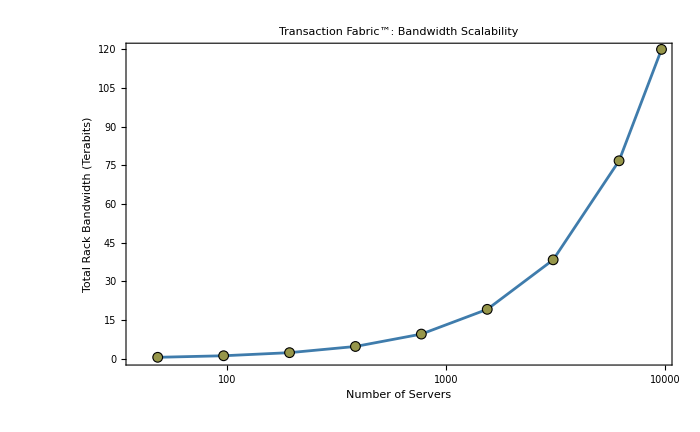

```mathematica
transactionFabricData={{48,0.6},{96,1.2},{192,2.4},{384,4.8},{768,9.6},{1536,19.2},{3072,38.4},{6144,76.8},{9600,120.0}};
scalabilityPlot=ListLogLinearPlot[transactionFabricData,Joined->True,PlotStyle->Directive[RGBColor["#3F7CAC"],AbsoluteThickness[2]],PlotMarkers->{Graphics[{RGBColor[0.59,0.59,0.29],EdgeForm[Black],Disk[]}],Medium},Frame->True,FrameLabel->{"Number of Servers","Total Rack Bandwidth (Terabits)"},LabelStyle->Directive[14,FontFamily->"Myriad Pro"],FrameStyle->Directive[Black,AbsoluteThickness[1]],GridLines->{Automatic,Automatic},PlotLabel->Style["Transaction Fabric™: Bandwidth Scalability",18,FontFamily->"Myriad Pro"],ImageSize->700,BaseStyle->FontFamily->"Myriad Pro"];
scalabilityPlot
```

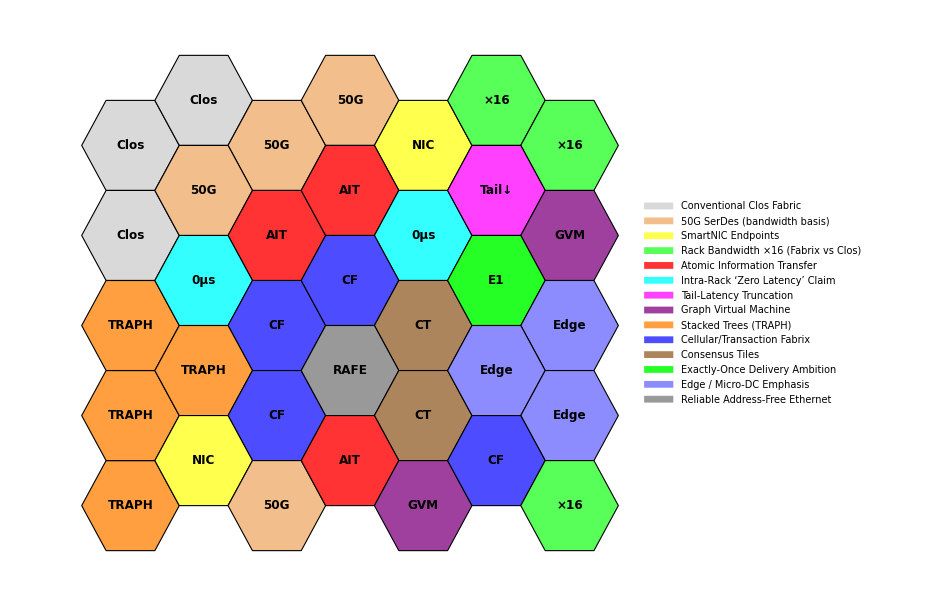

```mathematica
ClearAll[ThemeHexGrid];
Options[ThemeHexGrid]:={"CellSize"->100,"LabelCells"->True,"ShowLegend"->True};
themeColors=Association[CellularFabrix->Lighter[Blue,.3],AIT->Lighter[Red,.2],GVM->Lighter[Purple,.25],TRAPH->Lighter[Orange,.25],ConsensusTiles->Lighter[Brown,.2],ExactlyOnce->Lighter[Green,.15],TailTruncation->Lighter[Magenta,.25],ZeroLatency->Lighter[Cyan,.2],RAFE->Lighter[Gray,.2],SmartNIC->Lighter[Yellow,.3],SerDes50G->RGBColor[0.95,0.75,0.55],Clos->Lighter[Black,.85],RackBW16x->Lighter[Green,.35],Edge->Lighter[Blue,0.55]];
themeAbbrev=Association[CellularFabrix->"CF",AIT->"AIT",GVM->"GVM",TRAPH->"TRAPH",ConsensusTiles->"CT",ExactlyOnce->"E1",TailTruncation->"Tail↓",ZeroLatency->"0µs",RAFE->"RAFE",SmartNIC->"NIC",SerDes50G->"50G",Clos->"Clos",RackBW16x->"×16",Edge->"Edge"];
themeNames=Association[CellularFabrix->"Cellular/Transaction Fabrix",AIT->"Atomic Information Transfer",GVM->"Graph Virtual Machine",TRAPH->"Stacked Trees (TRAPH)",ConsensusTiles->"Consensus Tiles",ExactlyOnce->"Exactly-Once Delivery Ambition",TailTruncation->"Tail-Latency Truncation",ZeroLatency->"Intra-Rack ‘Zero Latency’ Claim",RAFE->"Reliable Address-Free Ethernet",SmartNIC->"SmartNIC Endpoints",SerDes50G->"50G SerDes (bandwidth basis)",Clos->"Conventional Clos Fabric",RackBW16x->"Rack Bandwidth ×16 (Fabrix vs Clos)",Edge->"Edge / Micro-DC Emphasis"];
ThemeHexGrid[board_,basis_List:{{1,0},{1/2,(√3)/2}},OptionsPattern[]]:=Module[{d1=Dimensions[board]⟦1⟧,d2=Dimensions[board]⟦2⟧,b1=basis⟦1⟧,b2=basis⟦2⟧,hex={{0,0},basis⟦1⟧,basis⟦1⟧+basis⟦2⟧,2 basis⟦2⟧,2 basis⟦2⟧-basis⟦1⟧,basis⟦2⟧-basis⟦1⟧},labelQ=TrueQ[OptionValue["LabelCells"]],legendQ=TrueQ[OptionValue["ShowLegend"]],g,used,cols,lbls},g=Graphics[Table[Module[{t=board⟦i+1,j+1⟧,ofs=i (b1-2 b2)+If[EvenQ[j],1/2 (3 j) b1,((3 j)/2-1/2) b1+b2],poly},poly=Translate[Polygon[hex],ofs];{EdgeForm[Black],Lookup[themeColors,t,LightGray],poly,If[labelQ,Inset[Style[Lookup[themeAbbrev,t,ToString[t]],12,Black,Bold],ofs+Mean[hex]],Nothing]}],{i,0,d1-1},{j,0,d2-1}],ImageSize->Max[Dimensions[board]] OptionValue["CellSize"]];used=DeleteDuplicates[Flatten[board]];cols=Lookup[themeColors,used,LightGray];lbls=Lookup[themeNames,used,ToString/@used];If[legendQ,Legended[g,Placed[SwatchLegend[cols,lbls,LabelStyle->11],Right]],g]];
sampleTopics={{Clos,Clos,SerDes50G,SerDes50G,SmartNIC,RackBW16x,RackBW16x},{Clos,SerDes50G,AIT,AIT,ZeroLatency,TailTruncation,GVM},{TRAPH,ZeroLatency,CellularFabrix,CellularFabrix,ConsensusTiles,ExactlyOnce,Edge},{TRAPH,TRAPH,CellularFabrix,RAFE,ConsensusTiles,Edge,Edge},{TRAPH,SmartNIC,SerDes50G,AIT,GVM,CellularFabrix,RackBW16x}};
ThemeHexGrid[sampleTopics]
```

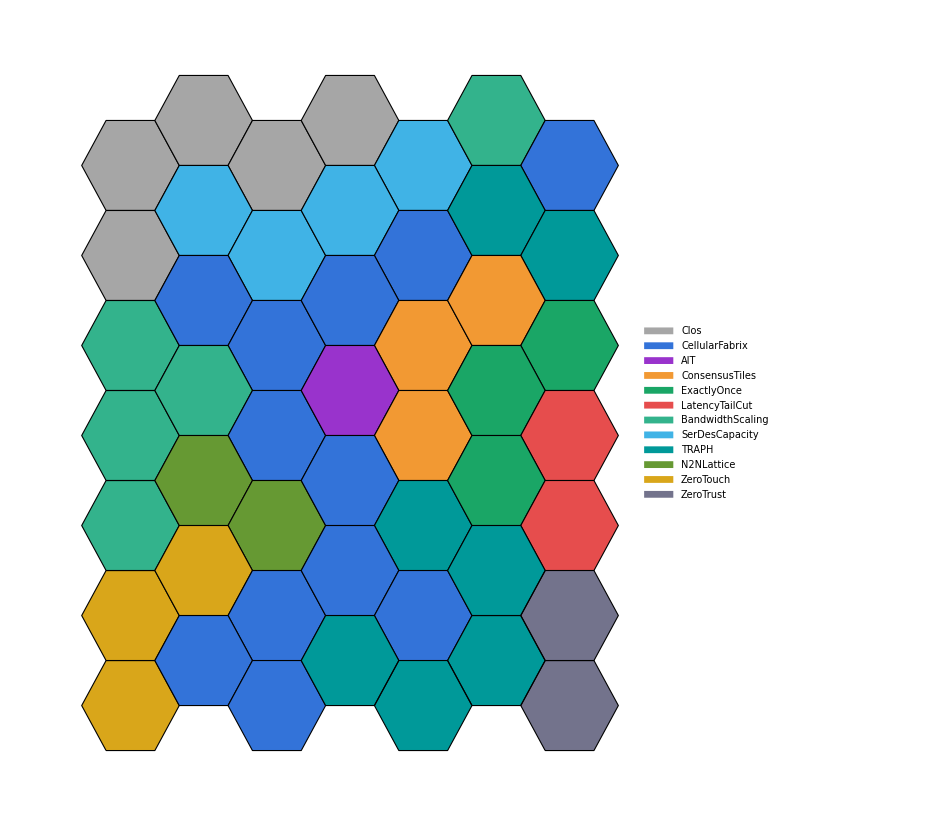

```mathematica
Options[TopologyBoard]:={"CellSize"->100,"ShowLegend"->True,"ThemeColors"->Automatic,"ThemeNotes"->Automatic};
TopologyBoard[themes_,basis_List:{{1,0},{1/2,(√3)/2}},OptionsPattern[]]:=Module[{defaultThemeColors,defaultThemeNotes,themeColors,themeNotes,d1,d2,b1,b2,hexagon,cellAt,cells,gfx,legend},defaultThemeColors=Association[Clos->GrayLevel[.65],CellularFabrix->RGBColor[0.20,0.45,0.85],AIT->RGBColor[0.60,0.20,0.80],ConsensusTiles->RGBColor[0.95,0.60,0.20],ExactlyOnce->RGBColor[0.10,.65,0.40],LatencyTailCut->RGBColor[0.90,0.30,0.30],BandwidthScaling->RGBColor[0.20,0.70,0.55],SerDesCapacity->RGBColor[0.25,0.70,0.90],TRAPH->RGBColor[0.00,0.60,0.60],N2NLattice->RGBColor[0.40,0.60,0.20],ZeroTouch->RGBColor[0.85,.65,0.10],ZeroTrust->RGBColor[0.45,0.45,0.55]];defaultThemeNotes=Association[Clos->"Conventional spine–leaf; drops/reordering/duplication yield long tails.",CellularFabrix->"Neighbor-to-neighbor graph fabric tuned for transactions.",AIT->"Atomic Information Transfer: reversible, no-copy, link-level common knowledge.",ConsensusTiles->"Built-in consensus plumbing for resilience and scale-out.",ExactlyOnce->"Link protocol advertises success/failure; enables exactly-once at endpoints.",LatencyTailCut->"Multicast + atomic link semantics truncate tail latency.",BandwidthScaling->"Fabrix claims order-of-magnitude higher effective east–west throughput.",SerDesCapacity->"Example: 96×50G SerDes; rack BW calcs and no breakout assumptions.",TRAPH->"Stacked Tree (TRee-grAPH) slices; in-order delivery on tree topologies.",N2NLattice->"Relative, address-free neighbor routing; add Kleinberg links to reduce hops.",ZeroTouch->"Auto discovery/config; adapts to cabling errors; no manual addressing.",ZeroTrust->"Programmable, tenant-safe slices under API control."];themeColors=Replace[OptionValue["ThemeColors"],Automatic->defaultThemeColors];themeNotes=Replace[OptionValue["ThemeNotes"],Automatic->defaultThemeNotes];{d1,d2}=Dimensions[themes];{b1,b2}=basis;hexagon={{0,0},b1,b1+b2,2 b2,2 b2-b1,b2-b1};cellAt[i_,j_]:=Module[{key,col,poly,tip},key=themes⟦i+1,j+1⟧;col=Lookup[themeColors,key,LightGray];poly=Translate[Polygon[hexagon],i (b1-2 b2)+If[EvenQ[j],1/2 (3 j) b1,((3 j)/2-1/2) b1+b2]];tip=Lookup[themeNotes,key,ToString[key,InputForm]];{EdgeForm[Black],col,Tooltip[poly,Row[{Style[key,Bold]," – ",tip}]]}];cells=Table[cellAt[i,j],{i,0,d1-1},{j,0,d2-1}];gfx=Graphics[cells,ImageSize->Max[Dimensions[themes]] OptionValue["CellSize"],PlotRangePadding->Scaled[.05],Background->White];legend=SwatchLegend[Lookup[themeColors,Keys[themeColors]],Keys[themeColors],LegendLayout->"Column"];If[TrueQ[OptionValue["ShowLegend"]],Legended[gfx,Placed[legend,Right]],gfx]];
sampleThemes={{Clos,Clos,Clos,Clos,SerDesCapacity,BandwidthScaling,CellularFabrix},{Clos,SerDesCapacity,SerDesCapacity,SerDesCapacity,CellularFabrix,TRAPH,TRAPH},{BandwidthScaling,CellularFabrix,CellularFabrix,CellularFabrix,ConsensusTiles,ConsensusTiles,ExactlyOnce},{BandwidthScaling,BandwidthScaling,CellularFabrix,AIT,ConsensusTiles,ExactlyOnce,LatencyTailCut},{BandwidthScaling,N2NLattice,N2NLattice,CellularFabrix,TRAPH,ExactlyOnce,LatencyTailCut},{ZeroTouch,ZeroTouch,CellularFabrix,CellularFabrix,CellularFabrix,TRAPH,ZeroTrust},{ZeroTouch,CellularFabrix,CellularFabrix,TRAPH,TRAPH,TRAPH,ZeroTrust}};
TopologyBoard[sampleThemes]
```

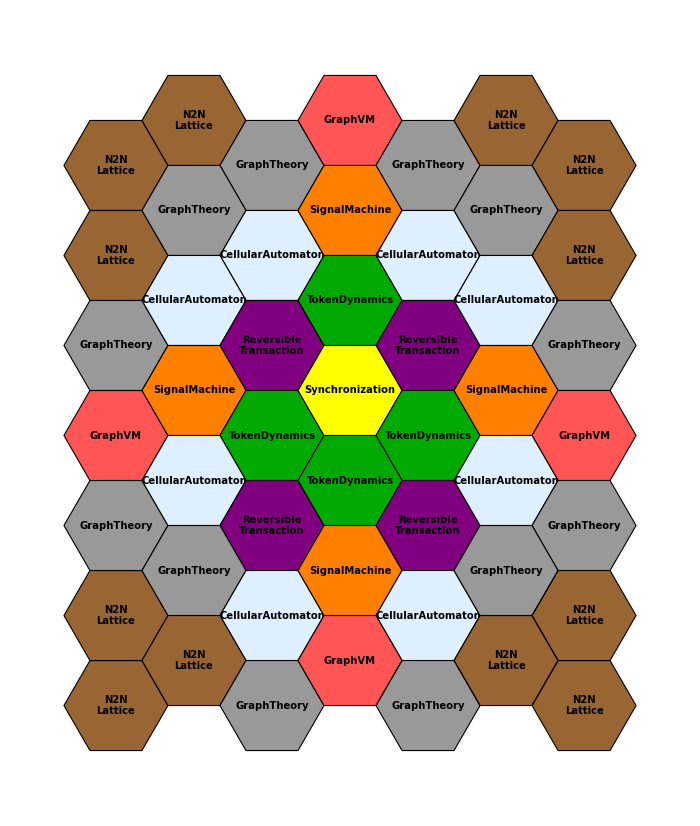

```mathematica
Options[VisualizeDaedalusConcepts]={"CellSize"->100};
VisualizeDaedalusConcepts[conceptGrid_,basis_List:{{1,0},{1/2,(√3)/2}},OptionsPattern[VisualizeDaedalusConcepts]]:=Graphics[Module[{conceptColors=Association[GraphTheory->GrayLevel[0.6],CellularAutomaton->LightBlue,SignalMachine->Orange,Synchronization->Yellow,ReversibleTransaction->Purple,TokenDynamics->Darker[Green],GraphVM->Lighter[Red],N2N_Lattice->Brown],d1=Dimensions[conceptGrid]⟦1⟧,d2=Dimensions[conceptGrid]⟦2⟧,b1=basis⟦1⟧,b2=basis⟦2⟧,hexagon={{0,0},basis⟦1⟧,basis⟦1⟧+basis⟦2⟧,2 basis⟦2⟧,2 basis⟦2⟧-basis⟦1⟧,basis⟦2⟧-basis⟦1⟧}},Table[With[{concept=conceptGrid⟦i+1,j+1⟧,pos=i (b1-2 b2)+If[EvenQ[j],1/2 (3 j) b1,((3 j)/2-1/2) b1+b2]},{EdgeForm[Black],conceptColors[concept],Translate[Polygon[hexagon],pos],Text[Style[StringReplace[ToString[concept],{"_"->"\n","Transaction"->"\nTransaction"}],Black,Bold,10],pos+b2]}],{i,0,d1-1},{j,0,d2-1}]],ImageSize->Max[Dimensions[conceptGrid]] OptionValue["CellSize"]]
daedaelusConceptGrid={{N2N_Lattice,N2N_Lattice,GraphTheory,GraphVM,GraphTheory,N2N_Lattice,N2N_Lattice},{N2N_Lattice,GraphTheory,CellularAutomaton,SignalMachine,CellularAutomaton,GraphTheory,N2N_Lattice},{GraphTheory,CellularAutomaton,ReversibleTransaction,TokenDynamics,ReversibleTransaction,CellularAutomaton,GraphTheory},{GraphVM,SignalMachine,TokenDynamics,Synchronization,TokenDynamics,SignalMachine,GraphVM},{GraphTheory,CellularAutomaton,ReversibleTransaction,TokenDynamics,ReversibleTransaction,CellularAutomaton,GraphTheory},{N2N_Lattice,GraphTheory,CellularAutomaton,SignalMachine,CellularAutomaton,GraphTheory,N2N_Lattice},{N2N_Lattice,N2N_Lattice,GraphTheory,GraphVM,GraphTheory,N2N_Lattice,N2N_Lattice}};
VisualizeDaedalusConcepts[daedaelusConceptGrid]
```

```mathematica
hierarchical1to1={{1000,1},{5000,5},{10000,19},{20000,37}};
hierarchical3to1={{1000,0.8},{5000,4},{10000,14.5},{20000,28}};
hierarchical7to1={{1000,0.5},{5000,3.5},{10000,13},{20000,25}};
fatTree1to1={{1000,0.5},{5000,2},{10000,3.5},{20000,7.5}};
ListLogLinearPlot[{hierarchical1to1,hierarchical3to1,hierarchical7to1,fatTree1to1},PlotTheme->"Marketing",PlotStyle->{Red,Green,Blue,Magenta},PlotLegends->Placed[{"1:1 Hierarchical","3:1 Hierarchical","7:1 Hierarchical","1:1 Fat-Tree"},Below],FrameLabel->{"Number of Hosts","Estimated Cost (USD Millions)"},PlotLabel->"Network Cost vs. Cluster Size and Oversubscription",InterpolationOrder->2]
```

-Graphics-

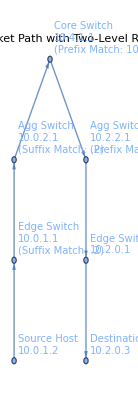

```mathematica
path={"Source Host\n10.0.1.2","Edge Switch\n10.0.1.1\n(Suffix Match: .2)","Agg Switch\n10.0.2.1\n(Suffix Match: .2)","Core Switch\n10.4.1.1\n(Prefix Match: 10.2.0.0/16)","Agg Switch\n10.2.2.1\n(Prefix Match: 10.2.0.0/24)","Edge Switch\n10.2.0.1","Destination Host\n10.2.0.3"};
Graph[Table[path⟦i⟧->path⟦i+1⟧,{i,1,Length[path]-1}],PlotLabel->"Example Packet Path with Two-Level Routing",VertexLabels->"Name",VertexLabelStyle->{10},GraphLayout->"LayeredDrawing"]
```

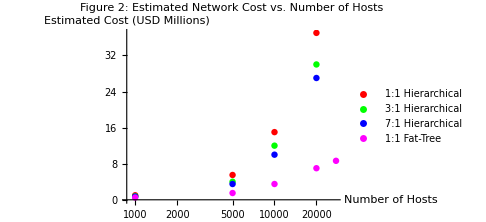

```mathematica
costData={{{1000,1},{5000,5.5},{10000,15},{20000,37}},{{1000,0.8},{5000,4},{10000,12},{20000,30}},{{1000,0.7},{5000,3.5},{10000,10},{20000,27}},{{1000,0.5},{5000,1.5},{10000,3.5},{20000,7},{27648,8.64}}};
ListLogLinearPlot[costData,PlotLabel->Style["Figure 2: Estimated Network Cost vs. Number of Hosts",Bold,16],AxesLabel->{"Number of Hosts","Estimated Cost (USD Millions)"},PlotLegends->{"1:1 Hierarchical","3:1 Hierarchical","7:1 Hierarchical","1:1 Fat-Tree"},PlotStyle->{Directive[Red,Thick],Directive[Green,Dashed],Directive[Blue,Dashed],Directive[Magenta,Thick]},GridLines->Automatic,ImageSize->Medium]
```

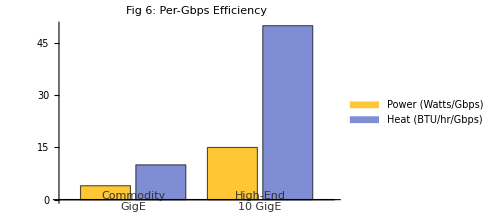
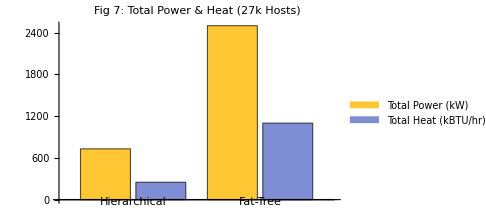
-Graphics- | -Graphics-

```mathematica
powerHeatPerGbps={Association["Label"->"Commodity\nGigE","Power"->4,"Heat"->15],Association["Label"->"High-End\n10 GigE","Power"->10,"Heat"->50]};
totalPowerHeat={Association["Design"->"Hierarchical","Power"->730,"Heat"->2500],Association["Design"->"Fat-Tree","Power"->250,"Heat"->1100]};
Grid[{{BarChart[{powerHeatPerGbps⟦All,"Power"⟧,powerHeatPerGbps⟦All,"Heat"⟧},PlotLabel->Style["Fig 6: Per-Gbps Efficiency",Bold,14],ChartLabels->{powerHeatPerGbps⟦All,"Label"⟧,None},ChartLegends->{"Power (Watts/Gbps)","Heat (BTU/hr/Gbps)"},ImageSize->Medium,LabelStyle->{GrayLevel[0.2],Bold}],BarChart[{totalPowerHeat⟦All,"Power"⟧,totalPowerHeat⟦All,"Heat"⟧},PlotLabel->Style["Fig 7: Total Power & Heat (27k Hosts)",Bold,14],ChartLabels->{totalPowerHeat⟦All,"Design"⟧,None},ChartLegends->{"Total Power (kW)","Total Heat (kBTU/hr)"},ImageSize->Medium,LabelStyle->{GrayLevel[0.2],Bold}]}}]
```

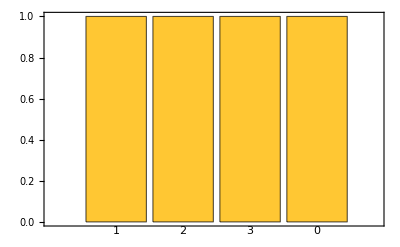
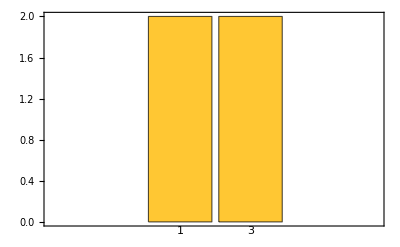
Aggregation index from edge (aSel) | -Graphics-
True row from aggregation (rSel) | -Graphics-

```mathematica
ClearAll[SuffixSpread];
SuffixSpread[k_Integer?EvenQ,eS_Integer?NonNegative]:=Module[{hids=hostIDs[k],aVals,rVals,aCounts,rCounts},aVals=(Mod[#1-2+eS,k/2]&)/@hids;rVals=(Mod[#1-2+#2,k/2]&)@@@Transpose[{hids,aVals}];aCounts=Counts[aVals];rCounts=Counts[rVals];Grid[{{Style["Aggregation index from edge (aSel)",Bold],BarChart[Values[aCounts],ChartLabels->Placed[Keys[aCounts],Below],Frame->True]},{Style["True row from aggregation (rSel)",Bold],BarChart[Values[rCounts],ChartLabels->Placed[Keys[rCounts],Below],Frame->True]}}]];
SuffixSpread[8,1]
```

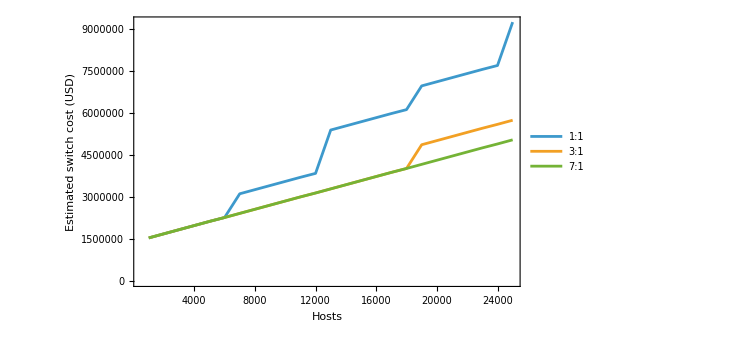

```mathematica
ClearAll[HierCostEstimate];
HierCostEstimate[hosts_,over_:3,edgePorts_:48,edgeCost_:7000,aggPorts10_:128,aggCost10_:700000]:=Module[{edges,uplinksPerEdge,aggNeeded,coreNeeded},edges=Ceiling[hosts/edgePorts];uplinksPerEdge=1/over;aggNeeded=Ceiling[(edges uplinksPerEdge)/aggPorts10];coreNeeded=Ceiling[aggNeeded/2];edges edgeCost+(aggNeeded+coreNeeded) aggCost10];
ListLinePlot[Table[{n,HierCostEstimate[n,over]},{over,{1,3,7}},{n,1000,25000,1000}],PlotLegends->Placed[{"1:1","3:1","7:1"},Right],Frame->True,FrameLabel->{"Hosts","Estimated switch cost (USD)"},PlotRange->All,ImageSize->550]
```

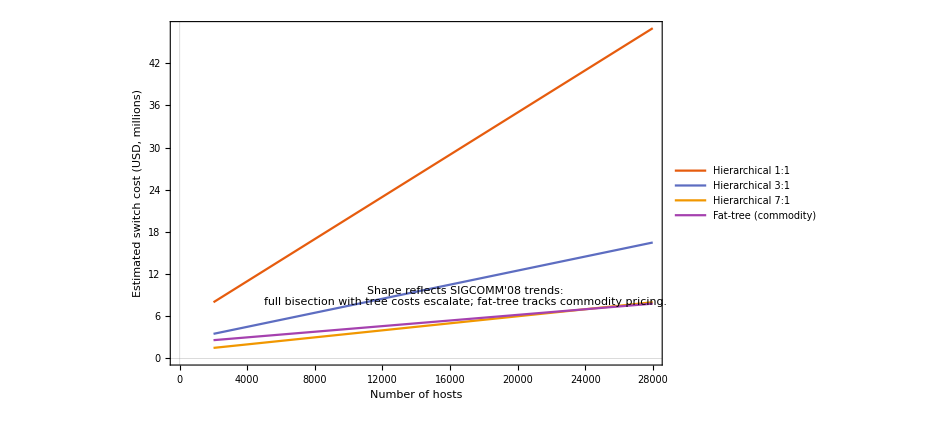

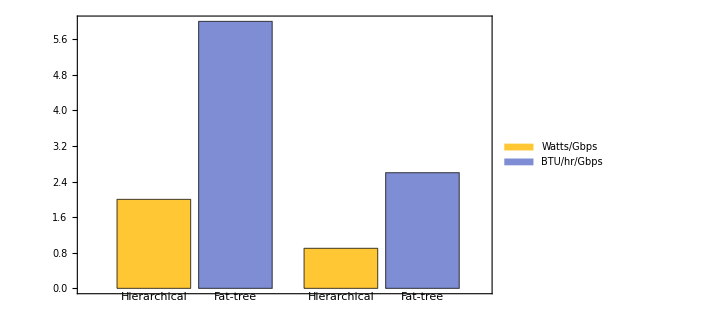
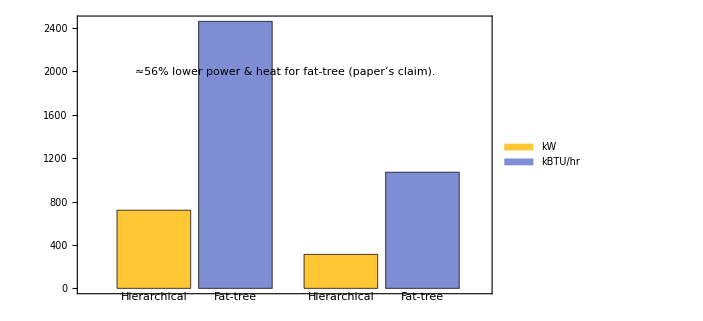
Normalized (per-Gbps) power & heat | -Graphics-
Aggregate totals (≈27k hosts) | -Graphics-

```mathematica
ClearAll[FatTreeIDs,FatTreeEdges,FatTreeCoordinates,FatTreeGraph,HostID,EdgeID,AggID,CoreID,PrettyLabel,PodColor,ShowAllShortestPaths,TwoLevelPath,EcmpPath,ScheduledPaths,RandomPairs,LinkLoad,LinkLoadPlot,BisectionExperiment,OversubscriptionCostPlot,PowerHeatComparisonPlot];
HostID[p_,e_,h_]:=StringTemplate["H[p`1`,e`2`,h`3`]"][p,e,h];
EdgeID[p_,e_]:=StringTemplate["E[p`1`,e`2`]"][p,e];
AggID[p_,a_]:=StringTemplate["A[p`1`,a`2`]"][p,a];
CoreID[g_,j_]:=StringTemplate["C[g`1`,j`2`]"][g,j];
PrettyLabel[s_String]:=StringReplace[s,{"H["->"Host[","E["->"Edge[","A["->"Agg[","C["->"Core["}];
PodColor[k_][p_]:=ColorData["DarkRainbow"][p/(k-1.0)];
ClearAll[ParseHost];
ParseHost[s_String]:=ToExpression[StringReplace[s,{"H["->"{","]"->"}"}]];
TwoLevelPath[g_Graph,k_,srcHost_String,dstHost_String]:=Module[{half=k/2,{ps,es,hs}=ParseHost[srcHost]⟦1;;3⟧,{pd,ed,hd}=ParseHost[dstHost]⟦1;;3⟧,srcEdge=EdgeID[ps,es],dstEdge=EdgeID[pd,ed],upAgg,group,core,downAgg,pth},group=Mod[hd,half];upAgg=AggID[ps,Mod[hd+es,half]];core=CoreID[group,Mod[es,half]];downAgg=AggID[pd,group];pth={srcHost,srcEdge,upAgg,core,downAgg,dstEdge,dstHost};If[AllTrue[Partition[pth,2,1],EdgeQ[g,UndirectedEdge@@#1]&],pth,$Failed]];
EcmpPath[g_Graph,k_,srcHost_String,dstHost_String]:=Module[{half=k/2,{ps,es,hs}=ParseHost[srcHost]⟦1;;3⟧,{pd,ed,hd}=ParseHost[dstHost]⟦1;;3⟧,h=Mod[Hash[srcHost<>"->"<>dstHost,"UnsignedInteger32"],half^2],group=Quotient[h,half],j=Mod[h,half],srcEdge=EdgeID[ps,es],dstEdge=EdgeID[pd,ed],upAgg=AggID[ps,Mod[es+group,half]],core=CoreID[group,j],downAgg=AggID[pd,group],pth},pth={srcHost,srcEdge,upAgg,core,downAgg,dstEdge,dstHost};If[AllTrue[Partition[pth,2,1],EdgeQ[g,UndirectedEdge@@#1]&],pth,$Failed]];
ShowAllShortestPaths[g_Graph,srcHost_String,dstHost_String]:=Module[{paths=FindPath[g,srcHost,dstHost,∞,All,All,"ShortestPaths"]},HighlightGraph[g,UndirectedEdge@@@Flatten[(Partition[#1,2,1]&)/@paths,1],GraphHighlightStyle->"DehighlightHide",ImageSize->900]];
ScheduledPaths[g_Graph,k_,pairs:{{_,_}..}]:=Module[{half=k/2,used=Association[],pathFor,makePath,res},makePath[{s_,d_}]:=Module[{cores=Flatten[Table[CoreID[group,j],{group,0,half-1},{j,0,half-1}]]},pathFor=SelectFirst[cores,Function[c,Module[{group=ToExpression[StringCases[c,"g"~~x:(DigitCharacter..):>x]⟦1⟧],ps=ParseHost[s]⟦1⟧,es=ParseHost[s]⟦2⟧,pd=ParseHost[d]⟦1⟧,ed=ParseHost[d]⟦2⟧,upAgg,downAgg,p},upAgg=AggID[ps,Mod[es+group,half]];downAgg=AggID[pd,group];p={s,EdgeID[ps,es],upAgg,c,downAgg,EdgeID[pd,ed],d};If[AllTrue[Partition[p,2,1],EdgeQ[g,UndirectedEdge@@#1]&]&&!TrueQ[used[c]],used[c]=True;p,Nothing]]],Function[_,Module[{p=EcmpPath[g,k,s,d]},If[p===$Failed,Nothing,p]]]];pathFor];res=AssociationThread[pairs,makePath/@pairs];res];
RandomPairs[hosts_List]:=Module[{dst=RandomSample[hosts]},Thread[hosts->dst]/.Rule->List];
LinkLoad[paths_Association]:=Module[{edges=Flatten[UndirectedEdge@@@(Partition[#1,2,1]&)/@Values[paths],1]},Association[Tally[edges]]];
LinkLoadPlot[load_Association,title_:"Per-link load (flows)"]:=Module[{data=Normal[load],pairs,counts},pairs=ToString/@Normal/@data⟦All,1⟧;counts=data⟦All,2⟧;BarChart[counts,ChartLabels->Placed[pairs,{0.5,0.0}],ChartLayout->"Stacked",PlotRange->All,ImageSize->1000,Frame->True,FrameLabel->{"Edge (u<->v)","Flow count"},PlotLabel->Style[title,13,Bold]]];
OversubscriptionCostPlot[]:=Module[{hosts=Range[2000,28000,2000],costTree11,costTree3x,costTree7x,costFat},costTree11=0.0015 hosts+5;costTree3x=0.0005 hosts+2.5;costTree7x=0.00025 hosts+1.0;costFat=0.0002 hosts+2.2;ListLinePlot[Transpose/@{{hosts,costTree11},{hosts,costTree3x},{hosts,costTree7x},{hosts,costFat}},PlotLegends->{"Hierarchical 1:1","Hierarchical 3:1","Hierarchical 7:1","Fat-tree (commodity)"},Frame->True,FrameLabel->{"Number of hosts","Estimated switch cost (USD, millions)"},ImageSize->700,PlotTheme->"Scientific",Epilog->{Inset[Style["Shape reflects SIGCOMM'08 trends:\nfull bisection with tree costs escalate; fat-tree tracks commodity pricing.",11],Scaled[{.6,.2}]]}]];
PowerHeatComparisonPlot[]:=Module[{wattsPerGbps=Association["Hierarchical"->2.0,"Fat-tree"->0.9],btuPerGbps=Association["Hierarchical"->6.0,"Fat-tree"->2.6],totalKW=Association["Hierarchical"->720.,"Fat-tree"->313.],totalKBTU=Association["Hierarchical"->2460.,"Fat-tree"->1070.]},Grid[{{Style["Normalized (per-Gbps) power & heat",12,Bold],BarChart[{{wattsPerGbps["Hierarchical"],btuPerGbps["Hierarchical"]},{wattsPerGbps["Fat-tree"],btuPerGbps["Fat-tree"]}},ChartLabels->Placed[{"Hierarchical","Fat-tree"},Below],ChartLegends->{"Watts/Gbps","BTU/hr/Gbps"},Frame->True,ImageSize->520,PlotRange->All]},{Style["Aggregate totals (≈27k hosts)",12,Bold],BarChart[{{totalKW["Hierarchical"],totalKBTU["Hierarchical"]},{totalKW["Fat-tree"],totalKBTU["Fat-tree"]}},ChartLabels->Placed[{"Hierarchical","Fat-tree"},Below],ChartLegends->{"kW","kBTU/hr"},Frame->True,ImageSize->520,PlotRange->All,Epilog->{Inset[Style["≈56% lower power & heat for fat-tree (paper’s claim).",11],Scaled[{0.5,.8}]]}]}},Spacings->{2,2}]];
OversubscriptionCostPlot[]
PowerHeatComparisonPlot[]
```

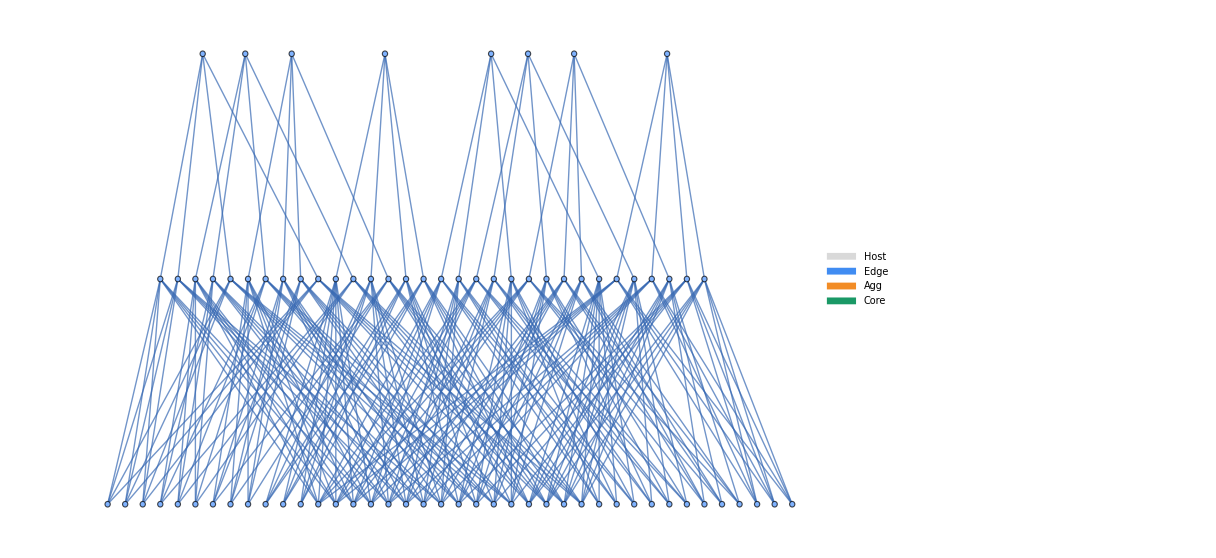
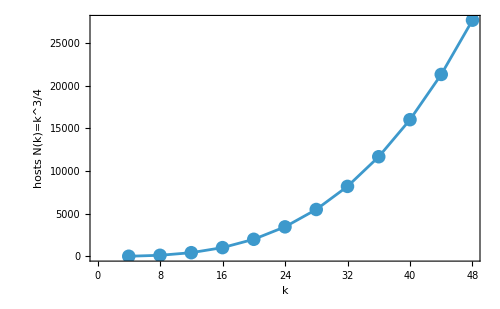
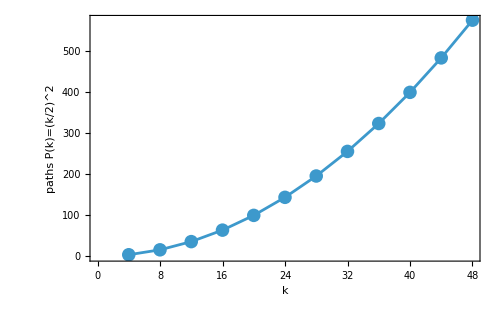
-Graphics-

Fat-tree capacity & path multiplicity
-Graphics--Graphics-

```mathematica
ClearAll[hostCount,pathMultiplicity,layerColor,layerOrder,tag,tidyLabel];
hostCount[k_Integer?EvenQ]:=k^3/4;
pathMultiplicity[k_Integer?EvenQ]:=(k/2)^2;
layerOrder=Association["Host"->1,"Edge"->2,"Agg"->3,"Core"->4];
layerColor=Association["Host"->Lighter[Gray,.7],"Edge"->RGBColor[0.25,0.55,0.95],"Agg"->RGBColor[0.95,0.55,0.15],"Core"->RGBColor[0.10,0.60,0.40]];
tag[type_,p_,s_:None]:=Switch[type,"Host",ToString[Row[{"H[",p,",",s⟦1⟧,",",s⟦2⟧,"]"}]],"Edge",ToString[Row[{"E[",p,",",s,"]"}]],"Agg",ToString[Row[{"A[",p,",",s,"]"}]],"Core",ToString[Row[{"C[",s⟦1⟧,",",s⟦2⟧,"]"}]]];
tidyLabel[str_]:=StringReplace[str,{"H["->"H(","E["->"E(","A["->"A(","C["->"C(","]"->")"}];
ClearAll[FatTreeComponents];
FatTreeComponents[k_Integer?EvenQ]:=Module[{m=k/2,pods=k,hosts,edges,aggs,coreNodes,hostNodes,edgeNodes,aggNodes,ⅇ,A,C,H},ⅇ[p_,z_]:=tag["Edge",p,z];A[p_,z_]:=tag["Agg",p,z];C[i_,j_]:=tag["Core",None,{i,j}];H[p_,e_,h_]:=tag["Host",p,{e,h}];edgeNodes=Flatten[Table[ⅇ[p,z],{p,0,pods-1},{z,0,m-1}]];aggNodes=Flatten[Table[A[p,z],{p,0,pods-1},{z,0,m-1}]];coreNodes=Flatten[Table[C[i,j],{i,1,m},{j,1,m}]];hostNodes=Flatten[Table[H[p,e,h],{p,0,pods-1},{e,0,m-1},{h,1,m}]];hosts=Flatten[Table[Table[H[p,e,h]<->ⅇ[p,e],{h,1,m}],{p,0,pods-1},{e,0,m-1}]];edges=Flatten[Table[Table[ⅇ[p,e]<->A[p,a],{a,0,m-1}],{p,0,pods-1},{e,0,m-1}]];aggs=Flatten[Table[Table[A[p,a]<->C[a+1,j],{j,1,m}],{p,0,pods-1},{a,0,m-1}]];Association["Hosts"->hostNodes,"Edges"->edgeNodes,"Aggs"->aggNodes,"Cores"->coreNodes,"HostEdges"->hosts,"EdgeAggs"->edges,"AggCores"->aggs]];
ClearAll[FatTreeDiagram];
Options[FatTreeDiagram]={"ShowHosts"->False,"ImageSize"->900};
FatTreeDiagram[k_Integer?EvenQ,OptionsPattern[]]:=Module[{comp=FatTreeComponents[k],showH=TrueQ[OptionValue["ShowHosts"]],verts,eds,vstyle,vsizeRules,vstyleRules},verts=Join[If[showH,comp["Hosts"],{}],comp["Edges"],comp["Aggs"],comp["Cores"]];eds=Join[If[showH,comp["HostEdges"],{}],comp["EdgeAggs"],comp["AggCores"]];vstyle[name_String]:=Module[{layer},layer=Which[StringStartsQ[name,"H["]||StringStartsQ[name,"H("],"Host",StringStartsQ[name,"E["]||StringStartsQ[name,"E("],"Edge",StringStartsQ[name,"A["]||StringStartsQ[name,"A("],"Agg",StringStartsQ[name,"C["]||StringStartsQ[name,"C("],"Core",True,"Host"];{EdgeForm[Black],layerColor[layer]}];vstyleRules=(#1->vstyle[#1]&)/@verts;vsizeRules=(#1->If[StringStartsQ[#1,"H["]||StringStartsQ[#1,"H("],0.15,.3]&)/@verts;Graph[eds,VertexLabels->Placed[(#1->Style[tidyLabel[#1],9]&)/@verts,{Right,Center}],VertexStyle->vstyleRules,VertexSize->vsizeRules,GraphLayout->"LayeredDigraphEmbedding",ImageSize->OptionValue["ImageSize"]]];
ClearAll[ScalingPlots];
Options[ScalingPlots]={"KMax"->48,"Step"->4,"ImageSize"->500};
ScalingPlots[OptionsPattern[]]:=Module[{kmax=OptionValue["KMax"],step=OptionValue["Step"],ks,hosts,paths},ks=Select[Range[4,kmax,step],EvenQ];hosts=hostCount/@ks;paths=pathMultiplicity/@ks;Grid[{{Style["Fat-tree capacity & path multiplicity",13,Bold]},{Row[{ListLinePlot[Transpose[{ks,hosts}],Frame->True,FrameLabel->(Style[#1,12]&)/@{"k","hosts  N(k)=k^3/4"},Mesh->All,PlotMarkers->Automatic,ImageSize->OptionValue["ImageSize"]],Spacer[20],ListLinePlot[Transpose[{ks,paths}],Frame->True,FrameLabel->(Style[#1,12]&)/@{"k","paths  P(k)=(k/2)^2"},Mesh->All,PlotMarkers->Automatic,ImageSize->OptionValue["ImageSize"]]}]}},Spacings->{2,1}]];
ClearAll[randomFlows,assignCore,simulateLoads,TrafficDemo];
randomFlows[k_,n_]:=Module[{m=k/2},Table[With[{dstID=RandomInteger[{2,m+1}]},Association["dstID"->dstID]],{n}]];
assignCore["SinglePath"][k_,flow_]:=1;
assignCore["TwoLevel"][k_,flow_]:=Module[{m=k/2,m2=(k/2)^2,id=flow["dstID"]},1+Mod[id-2,m2]];
simulateLoads[k_Integer?EvenQ,flows_,mode_String]:=Module[{m2=(k/2)^2,coreChoice,counts,loads,effPerFlow,effAvg},coreChoice=assignCore[mode]@@@Transpose[{ConstantArray[k,Length[flows]],flows}];counts=Counts[coreChoice,{1}];loads=Table[Lookup[counts,i,0],{i,1,m2}];effPerFlow=1./((Lookup[counts,#1,1]&)/@coreChoice);effAvg=N[Mean[effPerFlow]];Association["CoreLoads"->loads,"AvgThroughputPerFlow"->effAvg]];
ClearAll[FatTreeLegend];
FatTreeLegend[]:=SwatchLegend[layerColor/@{"Host","Edge","Agg","Core"},{"Host","Edge","Agg","Core"},LegendLayout->"Column"];
fatTree8=Legended[FatTreeDiagram[8,"ShowHosts"->False],Placed[FatTreeLegend[],Right]];
scalePlots=ScalingPlots["KMax"->48,"Step"->4];
Column[{fatTree8,Spacer[10],scalePlots},Spacings->2]
```